# Cuaderno de Prácticas

## MATEMÁTICAS DISCRETAS

## Grado en Ingeniería Informática

## CURSO 2025/26

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas : 4

## Códigos

```mathematica
(*
Capitulo 8 Relaciones de Orden Ejemplo 8.7
*)
ORDEN[A_,R_]:=Module[{falloReflexiva,falloAntisimetrica,falloTransitiva},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
(*
Capitulo 9 Reticulo Ejemplo 9.1
*)
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
(*
Capitulo 9 Álgebras de Boole finitas Ejemplo 9.11.
*)
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},
maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales
]
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},
cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
infimo={};
Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo
]
RETICULODISTRIBUTIVO[A_,R_]:=Module[{distributive,i,j,k},distributivo=True;
Do[Do[Do[If[TrueQ[SUPREMO[A,Union[{A[[i]]},INFIMO[A,{A[[j]],A[[k]]},R]],R]==INFIMO[A,Union[SUPREMO[A,{A[[i]],A[[j]]},R],SUPREMO[A,{A[[i]],A[[k]]},R]],R]],,distributivo=False;];         
,{i,1,Length[A]}];
      ,{j,1,Length[A]}];
   ,{k,1,Length[A]}];
distributivo
]
COMPLEMENTADO[A_,R_]:=Module[{complementado,k},complementado=True;
Do[If[COMPLEMENTO[A,R,A[[k]]]=={},complementado=False],{k,1,Length[A]}];
complementado]
(*

*)
```

## Práctica 9

### Ejercicio 9.4

Sea D el conjunto formado por los divisores positivos del producto de los tres últimos dígitos no nulos de tu DNI con la relación de orden,
								a<=b <=> b|a
Comprobar:

```mathematica
A94=Divisors[6*8*2];
D94={};
For[i=1, i<=Length[A94],i++,
	For[j=1, j<=Length[A94],j++,
		If[Mod[A94[[i]],A94[[j]]]==0,
		AppendTo[D94,{A94[[i]],A94[[j]]}];
		]
	]
]
D94
```

{{1,1},{2,1},{2,2},{3,1},{3,3},{4,1},{4,2},{4,4},{6,1},{6,2},{6,3},{6,6},{8,1},{8,2},{8,4},{8,8},{12,1},{12,2},{12,3},{12,4},{12,6},{12,12},{16,1},{16,2},{16,4},{16,8},{16,16},{24,1},{24,2},{24,3},{24,4},{24,6},{24,8},{24,12},{24,24},{32,1},{32,2},{32,4},{32,8},{32,16},{32,32},{48,1},{48,2},{48,3},{48,4},{48,6},{48,8},{48,12},{48,16},{48,24},{48,48},{96,1},{96,2},{96,3},{96,4},{96,6},{96,8},{96,12},{96,16},{96,24},{96,32},{96,48},{96,96}}

a) Si es un conjunto ordenado

```mathematica
ORDEN[A94,D94]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

b) Si es un retículo

```mathematica
RETICULO[A94,D94]
```

True

c) Si es un álgera de Boole

```mathematica
MAXIMALES[A94,D94]
```

{1}

```mathematica
MINIMALES[A94,D94]
```

{96}

```mathematica
COMPLEMENTADO[A94,D94]
```

True

```mathematica
RETICULODISTRIBUTIVO[A94,D94]
```

True

Por tanto es un álgebra de Boole, ya que es un retículo distributivo y si es un retículo con elemento 0, elemento 1 y complementado.

### Ejercicio 9.5

Sea D el conjunto de las partes del conjunto formado por los tres últimos dígitos distintos de tu DNI con la relación de orden
					A ≤ B ⇔ A ⊆ B
Comprobar

```mathematica
A95=Subsets[{6,8,2}];
D95={};
For[i=1, i<=Length[A95],i++,
	For[j=1, j<=Length[A95],j++,
		If[SubsetQ[A95[[j]],A95[[i]]],
		AppendTo[D95,{A95[[i]],A95[[j]]}];
		]
	]
]
D95
```

{{{},{}},{{},{6}},{{},{8}},{{},{2}},{{},{6,8}},{{},{6,2}},{{},{8,2}},{{},{6,8,2}},{{6},{6}},{{6},{6,8}},{{6},{6,2}},{{6},{6,8,2}},{{8},{8}},{{8},{6,8}},{{8},{8,2}},{{8},{6,8,2}},{{2},{2}},{{2},{6,2}},{{2},{8,2}},{{2},{6,8,2}},{{6,8},{6,8}},{{6,8},{6,8,2}},{{6,2},{6,2}},{{6,2},{6,8,2}},{{8,2},{8,2}},{{8,2},{6,8,2}},{{6,8,2},{6,8,2}}}

a) Si es un conjunto ordenado

```mathematica
ORDEN[A95,D95]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

b) Si es un retículo

```mathematica
RETICULO[A95,D95]
```

True

c) Si es un álgebra de Boole

```mathematica
MAXIMALES[A95,D95]
```

{{6,8,2}}

```mathematica
MINIMALES[A95,D95]
```

{{}}

```mathematica
COMPLEMENTADO[A95,D95]
```

True

```mathematica
RETICULODISTRIBUTIVO[A95,D95]
```

True

Por tanto es un álgebra de Boole, ya que es un retículo distributivo y si es un retículo con elemento 0, elemento 1 y complementado.

d) Calcular el complementado del conjunto formado por los dos primeros dígitos

e) Calcular los átomos y sus complementos

### Ejercicio 9 Rel 3

Sean A={a,b,c}, B={1,2,3}, A1={a,b} y B1={2,3}. Definir, si existe, una aplicación biyectiva f:AxP(B1) -> P(A1)xB y hacer todas las comprobaciones explícitamente

```mathematica
A18={"a","b","c"};
B18={1,2,3};
A181={"a","b"};
B181={2,3};
Dominio=CARTESIANO[{A18,Subsets[B181]}];
Codominio=CARTESIANO[{Subsets[A181],B18}];
Dominio
Codominio
A=Dominio;
B=Codominio;
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

{{a,{}},{b,{}},{c,{}},{a,{2}},{b,{2}},{c,{2}},{a,{3}},{b,{3}},{c,{3}},{a,{2,3}},{b,{2,3}},{c,{2,3}}}

{{{},1},{{a},1},{{b},1},{{a,b},1},{{},2},{{a},2},{{b},2},{{a,b},2},{{},3},{{a},3},{{b},3},{{a,b},3}}

El conjunto imagen es: {{{},1},{{},2},{{},3},{{a},1},{{a},2},{{a},3},{{b},1},{{b},2},{{b},3},{{a,b},1},{{a,b},2},{{a,b},3}}

Es sobreyectiva

Es inyectiva

Es biyectiva

```mathematica
If[Length[Dominio]==Length[Codominio], (*Compruebo que dominio y codominio tienen los mismos elementos para poder definir una aplicación biyectiva*)
	For[i=1, i<=Length[Dominio], i++,
		f[Dominio[[i]]]=Codominio[[i]];
	]
	,
	Print["No se puede definir una aplicación biyectiva"];
]
```

## Práctica 7

### Ejercicio 8.1

Sea A={a,b,c,d,e}, consideramos la relación binaria R={(a,b),(b,c),(d,e)}

```mathematica
A81={"a","b","c","d","e"};
```

a) Completar la relación binaria R para que sea una relación de orden total

```mathematica
R81a={
{"a","a"},{"a","b"},{"a","c"},{"a","d"},{"a","e"},
{"b","b"},{"b","c"},{"b","d"},{"b","e"},
{"c","c"},{"c","e"},{"c","d"},
{"d","d"},{"d","e"},
{"e","e"}
};
AnalisisRB[A81,R81a]
```

R es reflexiva

R no es simétrica, falla en los pares: {{b,a},{c,a},{d,a},{e,a},{c,b},{d,b},{e,b},{e,c},{d,c},{e,d}}

R es transitiva

R es antisimétrica

R no es relación de equivalencia

R es una relación de orden

Diagrama de orden:

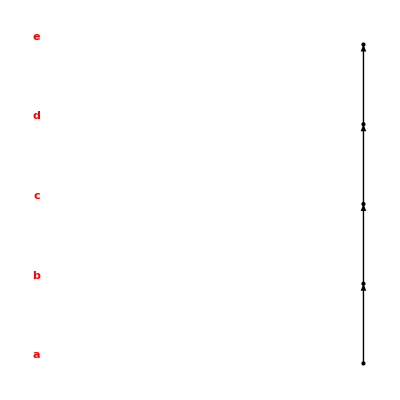

```mathematica
A=A81;
R=R81a;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Como se observa en el diagrama de Hasse el diagrama de orden es de una relación de orden total

b) Completar la relación binaria R para que sea reflexiva y transitiva, pero no sea simétrica y antisimétrica

```mathematica
R81b={
{"a","a"},{"a","b"},{"a","c"},{"a","d"},{"a","e"},
{"b","b"},{"b","c"},{"b","d"},{"b","e"},{"b","a"},
{"c","c"},{"c","e"},{"c","d"},
{"d","d"},{"d","e"},
{"e","e"}
};
AnalisisRB[A81,R81b]
```

R es reflexiva

R no es simétrica, falla en los pares: {{c,a},{d,a},{e,a},{c,b},{d,b},{e,b},{e,c},{d,c},{e,d}}

R es transitiva

R no es antisimétrica, falla en los pares: {{a,b},{b,a}}

R no es relación de equivalencia

R no es relación de orden

### Ejercicio 8.8

En el conjunto A={1,2,3,4} se establece la relación binaria 
R={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};
Justificar que es una relación de equivalencia y calcular el conjunto cociente. Comprobar que dicho conjunto de una partición de A.

```mathematica
A88={1,2,3,4};
R88={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};
AnalisisRB[A88,R88]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica, falla en los pares: {{2,3},{2,4},{3,2},{3,4},{4,2},{4,3}}

R es una relación de equivalencia

R no es relación de orden

```mathematica
COCIENTE[A88,R88]
```

{{1},{2,3,4}}

Demostración de que A es una partición

```mathematica
A1={1};
A2={2,3,4};
A1!={} && A2!={} (*ningun elemento de la particion es vacio*)
Intersection[A1,A2]=={} (*son disjuntos dos a dos, si hay mas elementos en la particion hay que hacer más comprobaciones*)
Union[A1,A2]==A88 (*La unión de todos da el total*)
```

True

True

True

### Ejercicio 8.14

Sea X={a,b,c,d,e,f} junto con la ordenación dada por el siguiente diagrama:
-Graphics-
Sea Y={b,f,e} y Z={e,b,c,a} subconjunto de X. Se pide:

```mathematica
X814={"a","b","c","d","e","f"};
R814={{"f","f"},{"f","e"},{"f","d"},{"f","c"},{"f","b"},{"f","a"},{"e","e"},{"e","c"},{"e","b"},{"e","a"},{"d","d"},{"d","b"},
{"d","a"},{"b","b"},{"b","a"},{"a","a"},{"c","c"}};
Y814={"b","f","e"};
Z814={"e","b","c","a"};
```

a) Cotas superiores e inferiores de Y y de Z. ¿Existen supremo e ínfimo?

```mathematica
"Cota superior"
COTASSUPERIORES[X814,Y814,R814]
"Supremo"
SUPREMO[X814,Y814,R814]
"Cota inferior"
COTASINFERIORES[X814,Y814,R814]
"Infimo"
INFIMO[X814,Y814,R814]
```

Cota superior

{a,b}

Supremo

{b}

Cota inferior

{f}

Infimo

{f}

```mathematica
"Cota superior"
COTASSUPERIORES[X814,Z814,R814]
"Supremo"
SUPREMO[X814,Z814,R814]
"Cota inferior"
COTASINFERIORES[X814,Z814,R814]
"Infimo"
INFIMO[X814,Z814,R814]
```

Cota superior

{}

Supremo

{}

Cota inferior

{e,f}

Infimo

{e}

b) Máximos y mínimos Y y Z

```mathematica
"Maximo"
MAXIMO[Y814,R814]
"Minimo"
MINIMO[Y814,R814]
```

Maximo

{b}

Minimo

{f}

```mathematica
"Maximo"
MAXIMO[Z814,R814]
"Minimo"
MINIMO[Z814,R814]
```

Maximo

{}

Minimo

{e}

C) Elementos máximales y minimales de X, Y, Z.

```mathematica
MAXIMALES[X814,R814]
MINIMALES[X814,R814]
```

{a,c}

{f}

```mathematica
MAXIMALES[Y814,R814]
MINIMALES[Y814,R814]
```

{b}

{f}

```mathematica
MAXIMALES[Z814,R814]
MINIMALES[Z814,R814]
```

{c,a}

{e}

b) Representa con Mathematica el diagrama de orden de X, Y y Z

Diagrama de orden:

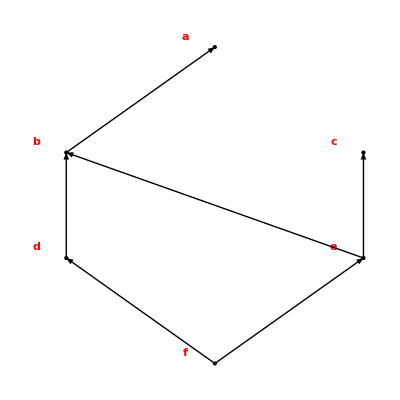

```mathematica
A=X814;
R=R814;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Diagrama de orden:

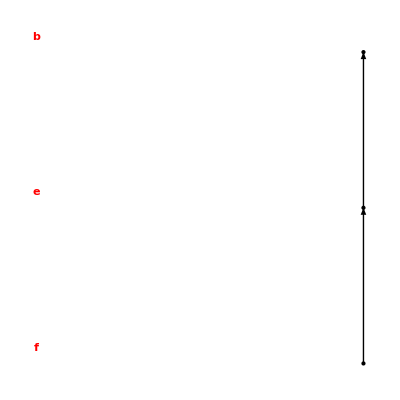

```mathematica
A=Y814;
R={{"f","f"},{"f","e"},{"f","b"},{"e","e"},{"e","b"},{"b","b"}};
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Diagrama de orden:

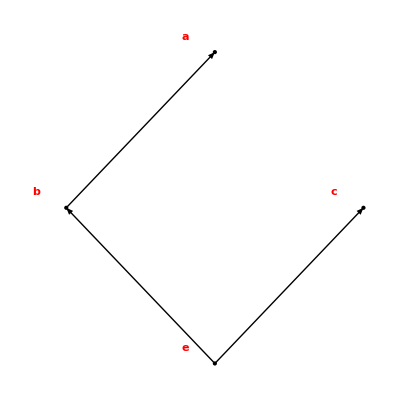

```mathematica
A=Z814;
R={{"e","e"},{"e","c"},{"e","b"},{"e","a"},{"b","b"},{"b","a"},{"a","a"},{"c","c"}};;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```